CreateDirectory::filex: "C:\\Users\\Petr\\Desktop\\Projects\\Programming Techniques\\shown results\\" already exists.

CreateDirectory::filex: "C:\\Users\\Petr\\Desktop\\Projects\\Programming Techniques\\shown results\\search\\" already exists.

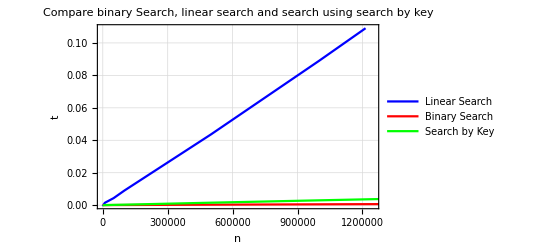

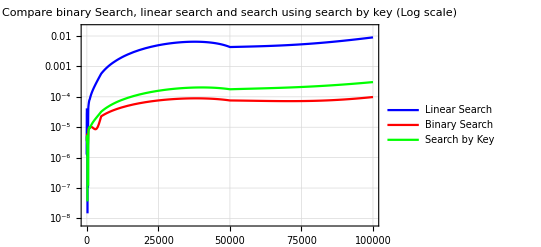

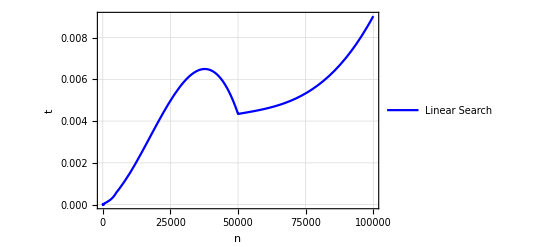

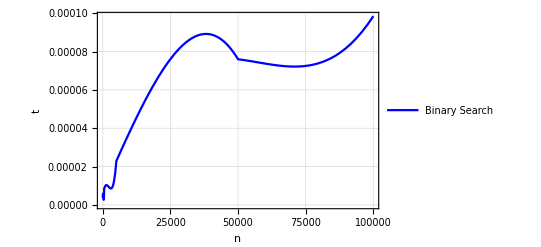

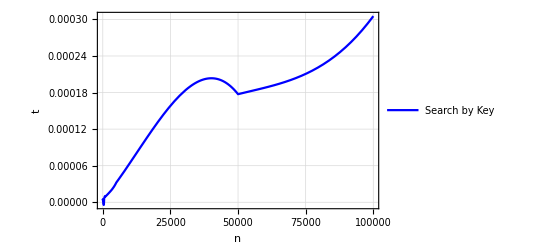

```mathematica
SetDirectory[NotebookDirectory[]];
workingDirectory = CreateDirectory["shown results"];
SetDirectory[workingDirectory];
file= OpenRead["../log_search.txt"];
workingDirectory = CreateDirectory["search"];
SetDirectory[workingDirectory];
filelist= ReadList[file,String];

mapSearchResults = filelist[[3;;;;4]];
binarySearchResults = filelist[[2;;;;4]];
linearSearchResults = filelist[[1;;;;4]];
linearSearchResults= Map[({StringSplit[#][[4]],StringSplit[#][[7]]})&,linearSearchResults];
binarySearchResults= Map[({StringSplit[#][[4]],StringSplit[#][[7]]})&,binarySearchResults];
mapSearchResults= Map[({StringSplit[#][[4]],StringSplit[#][[7]]})&,mapSearchResults];
linearSearchResults= Map[({Read[StringToStream[#[[1]]],Number],Read[StringToStream[#[[2]]],Number]})&,linearSearchResults];
binarySearchResults= Map[({Read[StringToStream[#[[1]]],Number],Read[StringToStream[#[[2]]],Number]})&,binarySearchResults];
mapSearchResults= Map[({Read[StringToStream[#[[1]]],Number],Read[StringToStream[#[[2]]],Number]})&,mapSearchResults];
Plot1 = Show[ListPlot[linearSearchResults,Joined->True,PlotStyle->Blue,PlotLegends->{"Linear Search"},PlotLabel->"Compare binary Search, linear search and search using search by key", AxesLabel->{"n","t"},PlotTheme->"Detailed",ImageSize->Scaled[0.8]],ListPlot[binarySearchResults,Joined->True,PlotStyle->Red,PlotLegends->{"Binary Search"}],
ListPlot[mapSearchResults,Joined->True,PlotStyle->Green,PlotLegends->{"Search by Key"}]]
linearFunc = Interpolation[linearSearchResults];
binaryFunc = Interpolation[binarySearchResults];
mapFunc = Interpolation[mapSearchResults];
Plot2 = LogPlot[{linearFunc[x],binaryFunc[x], mapFunc[x]},{x,0,10^5},PlotStyle->{Blue,Red, Green},PlotLegends->{"Linear Search","Binary Search","Search by Key"},PlotLabel->"Compare binary Search, linear search and search using search by key (Log scale)",PlotTheme->"Detailed",ImageSize->Scaled[0.8]]
Plot3 = Plot[linearFunc[x],{x,0,10^5},PlotStyle->Blue,PlotLegends->{"Linear Search"},AxesLabel->{"n","t"},PlotTheme->"Detailed",ImageSize->Scaled[0.8]]
Plot4 = Plot[binaryFunc[x],{x,0,10^5},PlotStyle->Blue,PlotLegends->{"Binary Search"},AxesLabel->{"n","t"},PlotTheme->"Detailed",ImageSize->Scaled[0.8]]
Plot5 = Plot[mapFunc[x],{x,0,10^5},PlotStyle->Blue,PlotLegends->{"Search by Key"},AxesLabel->{"n","t"},PlotTheme->"Detailed",ImageSize->Scaled[0.8]]
```

```mathematica
Export["Comp1.gif",Plot1,ImageSize->2048];
Export["Comp2.gif",Plot2,ImageSize->2048];
Export["Linear.gif",Plot3,ImageSize->2048];
Export["Binary.gif",Plot4,ImageSize->2048];
Export["Map.gif",Plot5,ImageSize->2048];
```

```mathematica
grid = Grid[Transpose[{Join[{"Time"},binarySearchResults[[All,1]]],Join[{"Linear Search"},linearSearchResults[[All,2]]],Join[{"Binary Search"},binarySearchResults[[All,2]]],Join[{"Search by Key"},mapSearchResults[[All,2]]]}],Frame->All,Alignment->Left,Background->{None,{Yellow}},ItemStyle->Directive[FontSize->20,Bold]]
```

Time | Linear Search | Binary Search | Search by Key
5 | 0.0000195743 | 3.88553×10^-6 | 4.28874×10^-6
10 | 3.22572×10^-6 | 4.10546×10^-6 | 3.81222×10^-6
50 | 8.76077×10^-6 | 5.35177×10^-6 | 4.50868×10^-6
100 | 0.0000101537 | 5.86495×10^-6 | 3.92219×10^-6
500 | 0.0000434739 | 8.50418×10^-6 | 6.37813×10^-6
1000 | 0.0000822926 | 0.0000100804 | 9.12733×10^-6
5000 | 0.000575388 | 0.0000228366 | 0.0000323672
10000 | 0.00150366 | 0.0000383055 | 0.0000642945
50000 | 0.00434109 | 0.0000759511 | 0.000177305
100000 | 0.00902491 | 0.0000984578 | 0.000305381
500000 | 0.043626 | 0.000305381 | 0.00152874
1000000 | 0.0890311 | 0.000525096 | 0.00298698
5000000 | 0.46294 | 0.00235474 | 0.0143804

```mathematica
Export["TableSerch.gif",grid,ImageSize->{2048,720}];
Export["TableSeach.xls",grid,ImageSize->{2048,720}];
```